{{1.2179,56.8836},{1.62522,56.9358},{1.12292,59.3248},{1.90912,54.5091}}

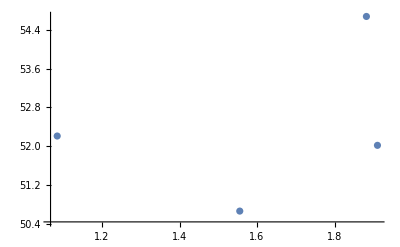

```mathematica
DATA=Table[{RandomReal[{1,2}],RandomReal[{50,60}]},4]
DATA ={{1.0840245923839322,52.20925027363165},{1.8822961467758659,54.67272155295678},{1.9108157057459443,52.01732920887136},{1.5553239385020956,50.66265855694875}};
ListPlot[DATA]
```

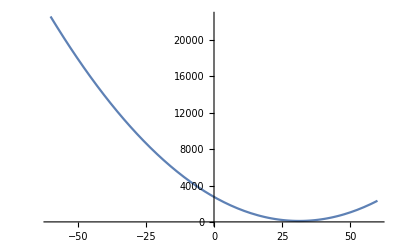

```mathematica
H1[W_, b_, x_]:=W x + b
H2[W_,x_]:=W x 
COST[W_]:=1/Length[DATA]∑_(i=1)^Length[DATA] (H2[W, DATA[[i]][[1]]]-DATA[[i]][[2]])^2
Plot[COST[W],{W,-60,60}]
GD[W0_,NN_,α_]:=Module[{W=W0},For[i=0,i<NN,i++,W=W-α (D[COST[WC], WC]/.WC->W)];W]
```

```mathematica
FindMinimum[COST[W],W]
D[COST[WC], WC]/.WC->70
GD[70,1000,0.1]
```

{104.191,{W→31.302}}

208.745

31.302